```mathematica
bincount=256;
tf=Import["D:\\document\\work\\volume-visualiser\\transferfuncs\\nucleon.tfi","XML"];
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );
rgba=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
alpha=(#/255.&)/@a;
rgbcolors
intensity
```

{RGBColor[{0.6, 0., 1.}],RGBColor[{0.5058823529411764, 0.3529411764705882, 1.}],RGBColor[{0.5686274509803921, 0.3058823529411765, 0.8666666666666667}],RGBColor[{0.6745098039215687, 0.22745098039215686, 0.6470588235294118}],RGBColor[{1., 0., 0.}],RGBColor[{1., 0., 0.}],RGBColor[{1., 0., 0.}],RGBColor[{0.611764705882353, 0.38823529411764707, 0.}],RGBColor[{0.01568627450980392, 1., 0.}],RGBColor[{0.28627450980392155, 1., 0.00392156862745098}],RGBColor[{0.03137254901960784, 0.32156862745098036, 0.027450980392156862}],RGBColor[{0.21176470588235294, 0.996078431372549, 0.2}]}

{0.141155,0.152678,0.172715,0.185807,0.411943,0.43787,0.4782,0.501154,0.786437,0.846932,0.94993,0.989554}

```mathematica
data=Import["D:\\_data\\nucleon.tif","Image3D"];
Image3D[data,ColorFunction->rgbafunction]
```

```mathematica
Length[h[[2]]]
```

196

```mathematica
Length[Last[h]]
```

196

```mathematica
a=Flatten[ImageData[data]];
h=HistogramList[a,bincount];
intensityfunction=Range[0,1,1./(Length[Last[h]]-1)];
sum:=Total[Last[h]];
hist[i_]:=First@FirstPosition[First[h],_?(i<#&)]-1;
probability[i_]:=N[Last[h][[hist[i]]]/sum];
entropy[i_]:=Module[{p},p=probability[i];If[p≠0,-p*Log[p],0]];
intensityvalues=Range[0,1,1./(Length[Last[h]]-1)]
acc=Accumulate[Last[h]]
```

{0.,0.00512821,0.0102564,0.0153846,0.0205128,0.025641,0.0307692,0.0358974,0.0410256,0.0461538,0.0512821,0.0564103,0.0615385,0.0666667,0.0717949,0.0769231,0.0820513,0.0871795,0.0923077,0.0974359,0.102564,0.107692,0.112821,0.117949,0.123077,0.128205,0.133333,0.138462,0.14359,0.148718,0.153846,0.158974,0.164103,0.169231,0.174359,0.179487,0.184615,0.189744,0.194872,0.2,0.205128,0.210256,0.215385,0.220513,0.225641,0.230769,0.235897,0.241026,0.246154,0.251282,0.25641,0.261538,0.266667,0.271795,0.276923,0.282051,0.287179,0.292308,0.297436,0.302564,0.307692,0.312821,0.317949,0.323077,0.328205,0.333333,0.338462,0.34359,0.348718,0.353846,0.358974,0.364103,0.369231,0.374359,0.379487,0.384615,0.389744,0.394872,0.4,0.405128,0.410256,0.415385,0.420513,0.425641,0.430769,0.435897,0.441026,0.446154,0.451282,0.45641,0.461538,0.466667,0.471795,0.476923,0.482051,0.487179,0.492308,0.497436,0.502564,0.507692,0.512821,0.517949,0.523077,0.528205,0.533333,0.538462,0.54359,0.548718,0.553846,0.558974,0.564103,0.569231,0.574359,0.579487,0.584615,0.589744,0.594872,0.6,0.605128,0.610256,0.615385,0.620513,0.625641,0.630769,0.635897,0.641026,0.646154,0.651282,0.65641,0.661538,0.666667,0.671795,0.676923,0.682051,0.687179,0.692308,0.697436,0.702564,0.707692,0.712821,0.717949,0.723077,0.728205,0.733333,0.738462,0.74359,0.748718,0.753846,0.758974,0.764103,0.769231,0.774359,0.779487,0.784615,0.789744,0.794872,0.8,0.805128,0.810256,0.815385,0.820513,0.825641,0.830769,0.835897,0.841026,0.846154,0.851282,0.85641,0.861538,0.866667,0.871795,0.876923,0.882051,0.887179,0.892308,0.897436,0.902564,0.907692,0.912821,0.917949,0.923077,0.928205,0.933333,0.938462,0.94359,0.948718,0.953846,0.958974,0.964103,0.969231,0.974359,0.979487,0.984615,0.989744,0.994872,1.}

{17624,21076,23664,27740,29389,30881,32197,34432,35516,36409,37910,38622,39423,39959,41135,41636,42156,42680,43502,43894,44378,45183,45508,45888,46144,46826,47094,47366,47683,48303,48583,48787,49303,49519,49683,49927,50387,50655,50883,51057,51458,51690,51834,52146,52314,52510,52754,53094,53222,53407,53656,53836,53956,54140,54454,54614,54814,54947,55131,55331,55459,55691,55775,55895,56011,56275,56432,56576,56704,56920,57065,57157,57373,57549,57657,57766,57987,58067,58155,58231,58476,58556,58676,58896,59040,59132,59201,59389,59486,59594,59862,59950,60018,60114,60266,60366,60454,60530,60686,60831,60891,61079,61155,61220,61320,61548,61616,61729,61837,62021,62145,62217,62373,62441,62525,62609,62753,62845,62926,62998,63202,63318,63382,63570,63611,63732,63841,64069,64157,64233,64389,64465,64577,64685,64849,64949,65085,65193,65374,65482,65583,65859,65983,66091,66203,66531,66692,66912,67181,67681,67901,67957,68021,68045,68093,68145,68201,68201,68213,68233,68269,68301,68321,68361,68401,68425,68469,68501,68505,68513,68537,68541,68545,68569,68601,68613,68637,68645,68661,68685,68697,68717,68745,68761,68785,68805,68817,68817,68829,68829,68841,68849,68869,68897,68913,68921}

```mathematica
ListLinePlot[Transpose[{intensity,alpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"transfer function"]
```

-Graphics-

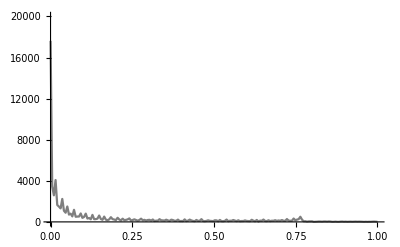

```mathematica
ListLinePlot[Transpose[{intensityvalues,Last[h]}],PlotRange->{{0,1},{0,20000}},ColorFunction->(GrayLevel[#]&),PlotLegends->"intensity histogram"]
```

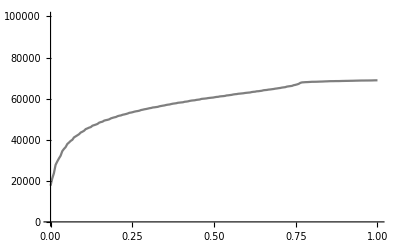

```mathematica
ListLinePlot[Transpose[{intensityvalues,acc}],PlotRange->{{0,1},{0,100000}},ColorFunction->(GrayLevel[#]&),PlotLegends->"cumulative intensity histogram"]
```

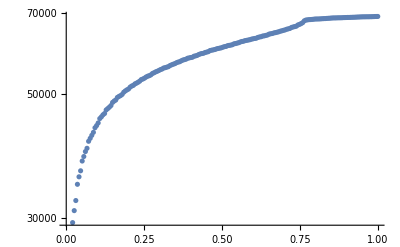

```mathematica
ListLogPlot[Transpose[{intensityvalues,acc}],PlotLegends->"cumulative intensity histogram with logarithmic scaling"]
```

```mathematica
ListLinePlot[Transpose[{intensityvalues,acc}],PlotRange->{{0,1},{0,100000}},ColorFunction->(GrayLevel[#]&),PlotLegends->"cumulative intensity histogram"]
```

-Graphics-

{0,0.,0.0431373,0.0431373,0.,0.,0.0509804,0.0509804,0.,0.,0.321569,0.32549,0.}

{0,0.,0.0431373,0.0431373,0.,0.,0.0509804,0.0509804,0.,0.,0.321569,0.32549,0.,0}

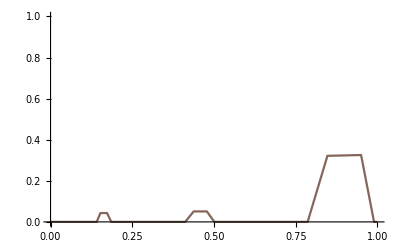

```mathematica
intensity0=intensity;
alpha0=alpha;
If[First[intensity0]>0,intensity0=Join[{0},intensity0];alpha0=Join[{0},alpha0]]
If[Last[intensity0]<1,intensity0=Join[intensity0,{1}];alpha0=Join[alpha0,{0}]]
ListLinePlot[Transpose[{intensity0,alpha0}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]
```

```mathematica
opacityfunction=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]
```

InterpolatingFunction[{{0., 1.}}, <>]

```mathematica
intensity0
alpha0
```

{0,0.141155,0.152678,0.172715,0.185807,0.411943,0.43787,0.4782,0.501154,0.786437,0.846932,0.94993,0.989554,1}

{0,0.,0.0431373,0.0431373,0.,0.,0.0509804,0.0509804,0.,0.,0.321569,0.32549,0.,0}

```mathematica
opacityfunction[0.015]
```

0.

```mathematica
Position[intensityvalues,_?(#>0.15267822&)]
```

{{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},{50},{51},{52},{53},{54},{55},{56},{57},{58},{59},{60},{61},{62},{63},{64},{65},{66},{67},{68},{69},{70},{71},{72},{73},{74},{75},{76},{77},{78},{79},{80},{81},{82},{83},{84},{85},{86},{87},{88},{89},{90},{91},{92},{93},{94},{95},{96},{97},{98},{99},{100},{101},{102},{103},{104},{105},{106},{107},{108},{109},{110},{111},{112},{113},{114},{115},{116},{117},{118},{119},{120},{121},{122},{123},{124},{125},{126},{127},{128},{129},{130},{131},{132},{133},{134},{135},{136},{137},{138},{139},{140},{141},{142},{143},{144},{145},{146},{147},{148},{149},{150},{151},{152},{153},{154},{155},{156},{157},{158},{159},{160},{161},{162},{163},{164},{165},{166},{167},{168},{169},{170},{171},{172},{173},{174},{175},{176},{177},{178},{179},{180},{181},{182},{183},{184},{185},{186},{187},{188},{189},{190},{191},{192},{193},{194},{195},{196}}

```mathematica
i=31
{intensityvalues[[i]],acc[[i]]}->opacityfunction[intensityvalues[[i]]]
```

31

{0.153846,48583}→0.0431373

```mathematica
Length[intensityvalues]
```

196

```mathematica
Length[Last[h]]
```

196

```mathematica
dataset=Table[{intensityvalues[[i]],acc[[i]]}->opacityfunction[intensityvalues[[i]]],{i,Length[intensityvalues]}]
```

{{0.,17624}→0.,{0.00512821,21076}→0.,{0.0102564,23664}→0.,{0.0153846,27740}→0.,{0.0205128,29389}→0.,{0.025641,30881}→0.,{0.0307692,32197}→0.,{0.0358974,34432}→0.,{0.0410256,35516}→0.,{0.0461538,36409}→0.,{0.0512821,37910}→0.,{0.0564103,38622}→0.,{0.0615385,39423}→0.,{0.0666667,39959}→0.,{0.0717949,41135}→0.,{0.0769231,41636}→0.,{0.0820513,42156}→0.,{0.0871795,42680}→0.,{0.0923077,43502}→0.,{0.0974359,43894}→0.,{0.102564,44378}→0.,{0.107692,45183}→0.,{0.112821,45508}→0.,{0.117949,45888}→0.,{0.123077,46144}→0.,{0.128205,46826}→0.,{0.133333,47094}→0.,{0.138462,47366}→0.,{0.14359,47683}→0.00911345,{0.148718,48303}→0.0283115,{0.153846,48583}→0.0431373,{0.158974,48787}→0.0431373,{0.164103,49303}→0.0431373,{0.169231,49519}→0.0431373,{0.174359,49683}→0.0377199,{0.179487,49927}→0.0208223,{0.184615,50387}→0.00392479,{0.189744,50655}→0.,{0.194872,50883}→0.,{0.2,51057}→0.,{0.205128,51458}→0.,{0.210256,51690}→0.,{0.215385,51834}→0.,{0.220513,52146}→0.,{0.225641,52314}→0.,{0.230769,52510}→0.,{0.235897,52754}→0.,{0.241026,53094}→0.,{0.246154,53222}→0.,{0.251282,53407}→0.,{0.25641,53656}→0.,{0.261538,53836}→0.,{0.266667,53956}→0.,{0.271795,54140}→0.,{0.276923,54454}→0.,{0.282051,54614}→0.,{0.287179,54814}→0.,{0.292308,54947}→0.,{0.297436,55131}→0.,{0.302564,55331}→0.,{0.307692,55459}→0.,{0.312821,55691}→0.,{0.317949,55775}→0.,{0.323077,55895}→0.,{0.328205,56011}→0.,{0.333333,56275}→0.,{0.338462,56432}→0.,{0.34359,56576}→0.,{0.348718,56704}→0.,{0.353846,56920}→0.,{0.358974,57065}→0.,{0.364103,57157}→0.,{0.369231,57373}→0.,{0.374359,57549}→0.,{0.379487,57657}→0.,{0.384615,57766}→0.,{0.389744,57987}→0.,{0.394872,58067}→0.,{0.4,58155}→0.,{0.405128,58231}→0.,{0.410256,58476}→0.,{0.415385,58556}→0.00676713,{0.420513,58676}→0.016851,{0.425641,58896}→0.0269348,{0.430769,59040}→0.0370186,{0.435897,59132}→0.0471024,{0.441026,59201}→0.0509804,{0.446154,59389}→0.0509804,{0.451282,59486}→0.0509804,{0.45641,59594}→0.0509804,{0.461538,59862}→0.0509804,{0.466667,59950}→0.0509804,{0.471795,60018}→0.0509804,{0.476923,60114}→0.0509804,{0.482051,60266}→0.0424262,{0.487179,60366}→0.0310366,{0.492308,60454}→0.019647,{0.497436,60530}→0.00825742,{0.502564,60686}→0.,{0.507692,60831}→0.,{0.512821,60891}→0.,{0.517949,61079}→0.,{0.523077,61155}→0.,{0.528205,61220}→0.,{0.533333,61320}→0.,{0.538462,61548}→0.,{0.54359,61616}→0.,{0.548718,61729}→0.,{0.553846,61837}→0.,{0.558974,62021}→0.,{0.564103,62145}→0.,{0.569231,62217}→0.,{0.574359,62373}→0.,{0.579487,62441}→0.,{0.584615,62525}→0.,{0.589744,62609}→0.,{0.594872,62753}→0.,{0.6,62845}→0.,{0.605128,62926}→0.,{0.610256,62998}→0.,{0.615385,63202}→0.,{0.620513,63318}→0.,{0.625641,63382}→0.,{0.630769,63570}→0.,{0.635897,63611}→0.,{0.641026,63732}→0.,{0.646154,63841}→0.,{0.651282,64069}→0.,{0.65641,64157}→0.,{0.661538,64233}→0.,{0.666667,64389}→0.,{0.671795,64465}→0.,{0.676923,64577}→0.,{0.682051,64685}→0.,{0.687179,64849}→0.,{0.692308,64949}→0.,{0.697436,65085}→0.,{0.702564,65193}→0.,{0.707692,65374}→0.,{0.712821,65482}→0.,{0.717949,65583}→0.,{0.723077,65859}→0.,{0.728205,65983}→0.,{0.733333,66091}→0.,{0.738462,66203}→0.,{0.74359,66531}→0.,{0.748718,66692}→0.,{0.753846,66912}→0.,{0.758974,67181}→0.,{0.764103,67681}→0.,{0.769231,67901}→0.,{0.774359,67957}→0.,{0.779487,68021}→0.,{0.784615,68045}→0.,{0.789744,68093}→0.0175773,{0.794872,68145}→0.0448368,{0.8,68201}→0.0720964,{0.805128,68201}→0.0993559,{0.810256,68213}→0.126615,{0.815385,68233}→0.153875,{0.820513,68269}→0.181135,{0.825641,68301}→0.208394,{0.830769,68321}→0.235654,{0.835897,68361}→0.262913,{0.841026,68401}→0.290173,{0.846154,68425}→0.317432,{0.851282,68469}→0.321734,{0.85641,68501}→0.32193,{0.861538,68505}→0.322125,{0.866667,68513}→0.32232,{0.871795,68537}→0.322515,{0.876923,68541}→0.322711,{0.882051,68545}→0.322906,{0.887179,68569}→0.323101,{0.892308,68601}→0.323296,{0.897436,68613}→0.323492,{0.902564,68637}→0.323687,{0.907692,68645}→0.323882,{0.912821,68661}→0.324077,{0.917949,68685}→0.324273,{0.923077,68697}→0.324468,{0.928205,68717}→0.324663,{0.933333,68745}→0.324858,{0.938462,68761}→0.325054,{0.94359,68785}→0.325249,{0.948718,68805}→0.325444,{0.953846,68817}→0.293323,{0.958974,68817}→0.251197,{0.964103,68829}→0.209071,{0.969231,68829}→0.166944,{0.974359,68841}→0.124818,{0.979487,68849}→0.082692,{0.984615,68869}→0.0405658,{0.989744,68897}→0.,{0.994872,68913}→0.,{1.,68921}→0.}

PredictorFunction[…]

{0.0831367,0.0653274,0.0525015,0.0310932,0.0236831,0.0171785,0.011689,0.000899008,-0.00325238,-0.00630214,-0.0128586,-0.0148645,-0.0173836,-0.0183743,-0.0230563,-0.0238451,-0.0247436,-0.025665,-0.0283053,-0.0284654,-0.0291562,-0.0316984,-0.0314722,-0.0315631,-0.0309389,-0.0327716,-0.0322166,-0.0316846,-0.0314122,-0.0328874,-0.0324016,-0.0314774,-0.0323527,-0.0314978,-0.0303429,-0.0296495,-0.0302018,-0.0296468,-0.028861,-0.0277638,-0.0279759,-0.0272132,-0.025943,-0.0256417,-0.0245099,-0.0235396,-0.0228462,-0.0227064,-0.0213439,-0.0203101,-0.0196455,-0.0185829,-0.0171743,-0.0161347,-0.015845,-0.0146671,-0.0137198,-0.0123862,-0.0113466,-0.0103994,-0.00903689,-0.00827422,-0.00665793,-0.00524927,-0.00381755,-0.00323944,-0.00204419,-0.000773965,0.000588546,0.0014435,0.00270796,0.00427811,0.00513307,0.00621873,0.00769659,0.00916869,0.00999481,0.0116342,0.0132274,0.0148898,0.0155775,0.0172169,0.0186255,0.0194574,0.0207276,0.0222978,0.0240006,0.025017,0.0265583,0.0280362,0.0285913,0.0301845,0.031893,0.0334401,0.0346642,0.0361882,0.0377814,0.0394439,0.0406449,0.0419093,0.0436641,0.0446805,0.0463429,0.0480688,0.0495928,0.0503786,0.0520871,0.0535362,0.055014,0.0560535,0.0574391,0.0591246,0.0603256,0.0620342,0.0636505,0.0652668,0.066537,0.0681072,0.0697408,0.0714263,0.0723504,0.0737822,0.0755138,0.0765302,0.0783945,0.0797974,0.0812695,0.0820553,0.0836485,0.0853109,0.0865119,0.0881744,0.0896292,0.091107,0.0922619,0.0937859,0.0951023,0.0965801,0.097637,0.0991148,0.100633,0.101142,0.102528,0.104005,0.10546,0.105669,0.106841,0.107673,0.108223,0.107439,0.108271,0.110049,0.111781,0.113743,0.115567,0.117368,0.119146,0.121246,0.123278,0.125263,0.127157,0.129073,0.131058,0.132928,0.134798,0.136761,0.138608,0.140524,0.142602,0.144656,0.146619,0.148696,0.150774,0.152736,0.154653,0.156684,0.158646,0.160701,0.16271,0.164672,0.166703,0.168689,0.170628,0.172637,0.174599,0.176584,0.178616,0.180717,0.182748,0.184849,0.186881,0.188935,0.190921,0.19286,0.194868,0.196923}

0.23438

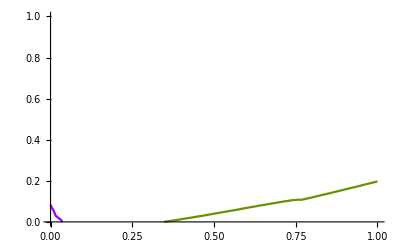

```mathematica
t0=AbsoluteTime[];
pr=Predict[dataset,Method->"LinearRegression"]
results=pr[{intensityvalues[[#]],acc[[#]]}]&/@Range[1,Length[intensityvalues]]
AbsoluteTime[]-t0
ListLinePlot[Transpose[{intensityvalues,results}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"LinearRegression"]
```

PredictorFunction[…]

{-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,0.00455672,0.0357244,0.0431373,0.0431373,0.0431373,0.0404286,0.0404286,0.0292711,0.00196239,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,0.00338356,0.00338356,0.011809,0.0319767,0.0420605,0.0490414,0.0490414,0.0509804,0.0509804,0.0509804,0.0509804,0.0509804,0.0509804,0.0509804,0.0367314,0.0253418,0.0139522,0.0139522,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18,0.00878865,0.0312071,0.0857262,0.0857262,0.112986,0.140245,0.194764,0.222024,0.222024,0.276543,0.303803,0.303803,0.321832,0.322027,0.322027,0.322222,0.322613,0.322808,0.322808,0.323003,0.323394,0.323394,0.323784,0.323784,0.32398,0.32437,0.32437,0.324565,0.324956,0.324956,0.325346,0.309384,0.27226,0.27226,0.188008,0.188008,0.103755,0.103755,0.0616289,-6.93889×10^-18,-6.93889×10^-18,-6.93889×10^-18}

0.296919

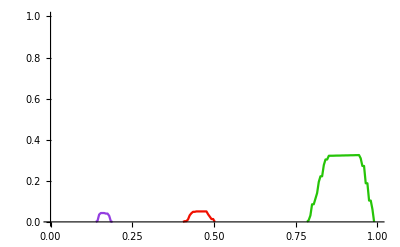

```mathematica
t0=AbsoluteTime[];
pr=Predict[dataset,Method->"NearestNeighbors"]
results=pr[{intensityvalues[[#]],acc[[#]]}]&/@Range[1,Length[intensityvalues]]
AbsoluteTime[]-t0
ListLinePlot[Transpose[{intensityvalues,results}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"NearestNeighbors"]
```

PredictorFunction[…]

{0.00603034,0.00523091,0.00383347,0.000843755,0.0000437616,-0.000361635,-0.000451126,-3.10216×10^-6,0.000447051,0.000903275,0.00201433,0.00253432,0.00320861,0.00360479,0.00491244,0.00532982,0.00579017,0.0062719,0.00727261,0.00756669,0.00802812,0.00909223,0.00928322,0.00957977,0.00964145,0.0105292,0.0106154,0.0107093,0.0108923,0.0116863,0.0117976,0.0117538,0.0123484,0.0123274,0.0121993,0.0122351,0.0127159,0.0128002,0.0128007,0.0126888,0.0130465,0.0130526,0.0128755,0.0130453,0.0129161,0.0128441,0.0128695,0.0130909,0.0128751,0.0127756,0.012805,0.0126926,0.0124583,0.0123521,0.012504,0.012346,0.0122661,0.0120524,0.011938,0.0118529,0.0116268,0.0115995,0.0112876,0.0110447,0.0107945,0.0108178,0.0106405,0.0104383,0.0102065,0.0101321,0.00992877,0.00963169,0.00955196,0.00940069,0.00913143,0.0088651,0.00878847,0.00847434,0.00817622,0.00786131,0.00782133,0.00751561,0.00727638,0.00719607,0.00699682,0.00671878,0.00640936,0.00628343,0.00602239,0.0057813,0.00577789,0.00551147,0.00522098,0.00497536,0.00481149,0.00457871,0.00433421,0.00407914,0.00393216,0.00377307,0.00351163,0.00341041,0.00317771,0.00293932,0.00274655,0.00269323,0.00247277,0.00230388,0.0021345,0.00203611,0.00188539,0.00169775,0.0015788,0.00140252,0.00124662,0.00110049,0.000989319,0.000862565,0.00074415,0.00063892,0.000554734,0.000468022,0.000401345,0.00032094,0.000300209,0.000269423,0.000264826,0.000176629,0.000224015,0.000326184,0.000359189,0.00055197,0.000740177,0.00099593,0.00117653,0.00159228,0.00199233,0.00259205,0.0030202,0.00388506,0.00498311,0.00527009,0.00660666,0.00835501,0.0104525,0.0109449,0.0132344,0.0153075,0.0171524,0.0162249,0.019194,0.0254761,0.0330602,0.0432122,0.0548708,0.0685659,0.0843239,0.104159,0.125556,0.14797,0.170296,0.192528,0.214286,0.234026,0.252378,0.269942,0.285809,0.301107,0.316213,0.329852,0.341226,0.350732,0.357435,0.360826,0.361278,0.359389,0.354921,0.348487,0.340023,0.329729,0.317973,0.30466,0.289891,0.273982,0.256806,0.238606,0.21955,0.199823,0.179277,0.158361,0.136947,0.115401,0.0937029,0.0720771,0.050909,0.0302833}

0.4843761

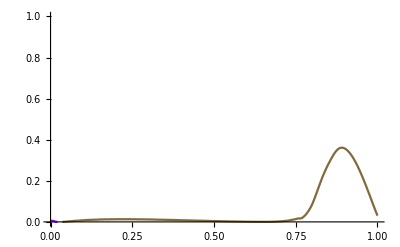

```mathematica
t0=AbsoluteTime[];
pr=Predict[dataset,Method->"NeuralNetwork"]
results=pr[{intensityvalues[[#]],acc[[#]]}]&/@Range[1,Length[intensityvalues]]
AbsoluteTime[]-t0
ListLinePlot[Transpose[{intensityvalues,results}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"NeuralNetwork"]
```

PredictorFunction[…]

{9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,0.000182269,0.000546807,0.00399469,0.00764007,0.0315804,0.0349998,0.0362004,0.0362004,0.0362004,0.0355798,0.0316164,0.016307,0.00183395,0.0000784957,0.0000784957,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,9.02056×10^-17,0.00256705,0.0077588,0.014686,0.0291003,0.0362214,0.0457334,0.0469162,0.0491816,0.0491816,0.0491816,0.0491816,0.0491816,0.0491816,0.0486856,0.0409428,0.0281063,0.0194334,0.0192056,0.00108011,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,0.000351546,0.00175773,0.0185165,0.0484823,0.0918537,0.0972148,0.128,0.174775,0.186601,0.196351,0.208617,0.26665,0.287183,0.313094,0.322025,0.322345,0.3224,0.322427,0.322578,0.322684,0.322771,0.322814,0.323123,0.323447,0.323886,0.324099,0.324233,0.324416,0.324448,0.324662,0.324864,0.324885,0.323031,0.311906,0.264895,0.242425,0.178928,0.132544,0.0702164,0.0598071,0.043007,0.043007,0.043007,0.043007}

1.329722

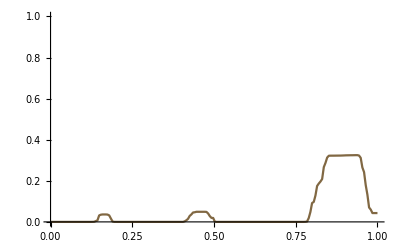

```mathematica
t0=AbsoluteTime[];
pr=Predict[dataset,Method->"RandomForest"]
results=pr[{intensityvalues[[#]],acc[[#]]}]&/@Range[1,Length[intensityvalues]]
AbsoluteTime[]-t0
ListLinePlot[Transpose[{intensityvalues,results}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"RandomForest"]
```